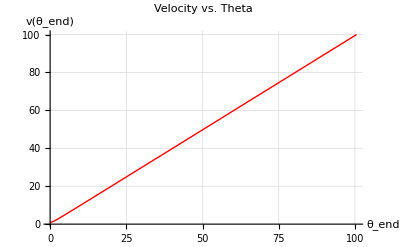

```mathematica
(*定义螺线参数*)a=0;
b=55/(2*Pi);
thetaEnd=2*Pi * 16; (*终点处的角度*)
vEnd=100; (*终点处的速度 cm/s*)

(*计算角速度 omega*)
omega=vEnd/(b*Sqrt[1+thetaEnd^2]);

(*定义速度方程*)
velocity[theta_]:=b*omega*Sqrt[1+theta^2]

(*绘制速度随角度变化的曲线*)
plot=Plot[velocity[theta],{theta,0,thetaEnd},AxesLabel->{"\!\(\*SubscriptBox[\(θ\), \(end\)]\)","v(\!\(\*SubscriptBox[\(θ\), \(end\)]\))"},PlotLabel->"Velocity vs. Theta",PlotRange->All,GridLines->Automatic,PlotStyle->{Thick,Red}];

Show[plot]

(*输出终点角速度以验证*)
{omega,velocity[thetaEnd]}
```

```mathematica
{(40 π)/(11 √(1+1024 π^2)),100}
```

{(40 π)/(11 √(1+1024 π^2)),100}

```mathematica
spiral=PolarPlot[b*theta,{theta,0,thetaMax},PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Thick,GridLines->Automatic];

(*显示图形*)
Show[spiral]
```

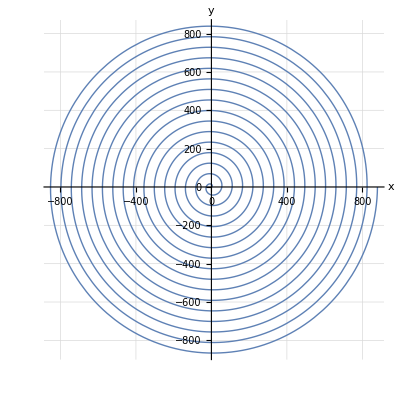
```mathematica
-Graphics-

(*Given polar equation*)r=b theta;

(*Convert to Cartesian*)
x=r Cos[theta];
y=r Sin[theta];

(*Substitute r=b theta*)
xSub=x/. r->b theta
ySub=y/. r->b theta

(*Solve for theta*)
thetaSol=Solve[xSub==x,theta,Reals]

(*Substitute theta into y equation*)
yEq=ySub/. First[thetaSol]

(*Simplify the equation*)
yFinal=Simplify[yEq]
```

-Graphics-

(55 theta Cos[theta])/(2 π)

(55 theta Sin[theta])/(2 π)

{{}}

(55 theta Sin[theta])/(2 π)

(55 theta Sin[theta])/(2 π)